```mathematica
Remove["Global`*"];

(* Generate clusters randomly. *)
Clear[n,α];
n=300;
n=240;
α={0.5,0.5};α/=Total[α];
α={0.25,0.75};α/=Total[α];
α={0.15,0.35,0.5};α/=Total[α];
α={1/3,1/3,1/3}//N;α/=Total[α];

Clear[numberOfClusters,clusterAssignment,clusterSizes,σ];
numberOfClusters=Length[α];
clusterAssignment=RandomChoice[α->Table[k,{k,1,numberOfClusters}],n]//Sort;
clusterSizes=Table[Count[clusterAssignment,k],{k,1,numberOfClusters}]
σ=Function[v,clusterAssignment[[v]]];

(* Construct the P-matrix. *)
Clear[p,P,r,c];

p12=0.045;p13=0.035;
p21=0.0125;p23=0.09;
p31=0.0175;p32=0.020;
p={
{1-p12-p13,p12,p13},
{p21,1-p21-p23,p23},
{p31,p32,1-p31-p32}
};

(*
p12=0.5;p21=0.32;
p={{1-p12,p12},{p21,1-p21}}//N;
*)

p12=0.4;p13=0.5;
p21=0.7;p23=0.2;
p31=0.6;p32=0.3;
p={
{1-p12-p13,p12,p13},
{p21,1-p21-p23,p23},
{p31,p32,1-p31-p32}
};

P=Table[0,{v,1,n},{w,1,n}];
For[r=1,r≤n,r++,
For[c=1,c≤n,c++,
P[[r,c]]=If[r≠c,1,0]*p[[σ[r],σ[c]]]/(clusterSizes[[σ[c]]]-If[σ[r]==σ[c],1,0]);
];
];

(* Check clusterability. *)
K=Length[α];
If[K==2,β=First[{β1,β2}/.Solve[{β1,β2}.p=={β1,β2}&&β1+β2==1,{β1,β2}]]];
If[K==3,β=First[{β1,β2,β3}/.Solve[{β1,β2,β3}.p=={β1,β2,β3}&&β1+β2+β3==1,{β1,β2,β3}]]];

Iab=Function[{a,b},
(1/α[[a]])^1*Sum[β[[a]]*p[[a,k]]*Log[p[[a,k]]/p[[b,k]]]+β[[k]]*p[[k,a]]*Log[(p[[k,a]]/p[[k,b]])*(α[[b]]/α[[a]])^1],{k,1,K}]
+(β[[b]]/α[[b]]-β[[a]]/α[[a]])
];

If[K==2,Iαβp=Min[Iab[1,2],Iab[2,1]];];
If[K==3,Iαβp=Min[Iab[1,2],Iab[1,3],Iab[2,1],Iab[2,3],Iab[3,1],Iab[3,2]];];

Print["I(α,β,p) = ",Iαβp];
If[Iαβp>0,
Print["Positive, so these parameters are clusterable."];
,
Print["NOT positive, so these parameters are NOT clusterable."];
];
```

{64,84,92}

I(α,β,p) = 0.271658

Positive, so these parameters are clusterable.

```mathematica
SpectralClustering=Function[{ASC,kSC},
DSC=DiagonalMatrix[Table[ASC[[r,;;]]//Total,{r,1,n}]];
LSC=MatrixPower[DSC,-1/2].ASC.MatrixPower[DSC,-1/2];

setOfEigenvectors=Eigenvectors[LSC]; (* These are normalized, and ordered in decreasing absolute value of their eigenvalues. *)
normsOfEigenvectors=Norm[#,2]&/@setOfEigenvectors;
kLargestEigenvectors=setOfEigenvectors[[1;;kSC]]; (* Hence the k-first are the "largest" eigenvectors. *)
XSC=Table[0,{r,1,n},{c,1,kSC}];
For[c=1,c≤kSC,c++,
For[r=1,r≤n,r++,
XSC[[r,c]]=kLargestEigenvectors[[c,r]];
];
];

YSC=0*XSC;
For[r=1,r≤n,r++,
YSC[[r,;;]]=XSC[[r,;;]]/Sqrt[Sum[XSC[[r,c]]^2,{c,1,kSC}]];
];

ClusteringComponents[YSC,kSC,1,Method->"KMeans"]
];

SpectralClusteringSVD=Function[{Phat,kSC},
{Uhat,Σhat,Vhat}=SingularValueDecomposition[Phat];
Rhat=Uhat[[;;,1;;numberOfClusters]].Σhat[[1;;numberOfClusters,1;;numberOfClusters]].Transpose[Vhat[[;;,1;;numberOfClusters]]];

(*
ClusteringComponents[Rhat,kSC,1,Method->"KMeans"]
*)

numberOfSeeds=5;
bestObjective=Infinity;
For[seed=1,seed≤numberOfSeeds,seed++,

(* Generate cluster structure with KMeans and the seed. *)
currentTuple=ClusteringComponents[Rhat,kSC,1,Method->"KMeans","RandomSeed"->seed];

centroids={};
For[cluster=1,cluster≤K,cluster++,
positions=Position[currentTuple,cluster]//Flatten;
AppendTo[centroids,Mean[Rhat[[positions,;;]]]];
];

objectiveValue=Sum[Norm[Rhat[[x]]-centroids[[currentTuple[[x]]]],2]^2,{x,1,n}];

If[objectiveValue<bestObjective,
bestObjective=objectiveValue;
bestAssignment=currentTuple;
];
];

bestAssignment
];
```

```mathematica
MissclassificationsStatistics=Function[recoveredClusterAssignment,

(* Find the best permutation of recovered clusters. *)
numberOfMissclassifiedVertices=Sum[If[recoveredClusterAssignment[[r]]≠clusterAssignment[[r]],1,0],{r,1,n}];

minNumberOfMissclassifiedVertices=n;
permutations=Permutations[Table[cluster,{cluster,1,numberOfClusters}]];
For[index=1,index≤Length[permutations],index++,
reordering=Table[
permutations[[index,recoveredClusterAssignment[[r]]]]
,
{r,1,n}];

numberOfMissclassifiedVertices=Sum[If[reordering[[r]]≠clusterAssignment[[r]],1,0],{r,1,n}];

If[numberOfMissclassifiedVertices≤minNumberOfMissclassifiedVertices,
minRecoveredClusterAssignment=reordering;
minNumberOfMissclassifiedVertices=numberOfMissclassifiedVertices;
];
];

{minNumberOfMissclassifiedVertices,minRecoveredClusterAssignment}
];
```

```mathematica
SuccessiveImprovements=Function[{Phat,Nhat,T,recoveredClusterAssignment},

recoveredClusterSizes=Table[Sum[If[recoveredClusterAssignment[[r]]==cluster,1,0],{r,1,n}],{cluster,1,numberOfClusters}];

(* Estimate pHat: the cluster parameters. *)
S0=Table[Position[recoveredClusterAssignment,cluster]//Flatten,{cluster,1,numberOfClusters}];

(*
(* Version 1. *)
pHat=Table[
Sum[
x=S0[[cr,xIndex]];y=S0[[cc,yIndex]];
Nhat[[x,y]]
,{xIndex,1,Length[S0[[cr]]]}
,{yIndex,1,Length[S0[[cc]]]}
]
/
Sum[
x=S0[[cr,xIndex]];
Nhat[[x,y]]
,{xIndex,1,Length[S0[[cr]]]}
,{y,1,n}
]
,{cr,1,numberOfClusters},{cc,1,numberOfClusters}];
*)

(* Version 2. *)
S0sizes=Table[Length[S0[[i]]],{i,1,Length[S0]}];
pHat=Table[
((S0sizes[[cc]]-If[cr==cc,1,0])/(S0sizes[[cr]]*S0sizes[[cc]]))
*Sum[
x=S0[[cr,xIndex]];y=S0[[cc,yIndex]];
Phat[[x,y]]
,{xIndex,1,Length[S0[[cr]]]}
,{yIndex,1,Length[S0[[cc]]]}
]
,{cr,1,numberOfClusters},{cc,1,numberOfClusters}];
(*pHat=p;*)
αHat=clusterSizes/n//N;
(*αHat=α;*)
βHat=(1/T)*Table[
Sum[
x=S0[[cr,xIndex]];
(*Total[Nhat[[;;,x]]]*) (* OK due to global balance! See remark on p. 83 notebook. *)
Total[Nhat[[x,;;]]]
,
{xIndex,1,Length[S0[[cr]]]}]
,{cr,1,numberOfClusters}
];

Print["Sample of input variable Nhat: ",Nhat[[1;;10,1;;10]]];

Print["The approximate parameters are ",{Dynamic[MatrixForm[pHat]],Dynamic[αHat],Dynamic[βHat]},
" while the exact ones are ",{MatrixForm[p],α},"."];

(* Improvement loop. *)
St=S0;
latestClusterAssignment=recoveredClusterAssignment;
latestClusterSizes=recoveredClusterSizes;
maxImprovements=Log[n];
(*maxImprovements=2;*)
Print["Improving cluster allocation: ",ProgressIndicator[Dynamic[(improvement-1)/(maxImprovements-1)]]];
Print["Executing improvement ",Dynamic[improvement],"... At ",Dynamic[N[100*(x-1)/(n-1),3]],"%."];
For[improvement=1,improvement≤maxImprovements,improvement++,

nextClusterAssignment={};
Stp1=Table[{},{c,1,numberOfClusters}];

For[x=1,x≤n,x++,

(*
(* Version 5 - Proven, reduced. *)
clusterShifts=
Table[
Sum[
clusterOfx=latestClusterAssignment[[x]];
clusterOfy=latestClusterAssignment[[y]];
If[y≠x,
0*Nhat[[x,y]]*Log[pHat[[cluster,clusterOfy]]]
+
1*Nhat[[y,x]]*Log[pHat[[clusterOfy,cluster]]]
,0
]
,{y,1,n}]
,{cluster,1,numberOfClusters}
];
(*Print["Cluster shift table: ",clusterShifts];*)
*)

(* Version 6. *)
clusterShifts=
Table[
Sum[
clusterOfx=latestClusterAssignment[[x]];
clusterOfy=latestClusterAssignment[[y]];
If[y≠x,
1*Nhat[[x,y]]*Log[pHat[[cluster,clusterOfy]]]
+
1*Nhat[[y,x]]*Log[pHat[[clusterOfy,cluster]]/αHat[[cluster]]^1]
,0
]
,{y,1,n}]
+1*(T/n)*(-βHat[[cluster]]/αHat[[cluster]])
(*
Sum[
clusterOfx=latestClusterAssignment[[x]];
clusterOfz=latestClusterAssignment[[z]];
If[y≠x&&z≠x&&clusterOfz==cluster,
-Nhat[[y,z]]/clusterSizes[[clusterOfz]]
,0
]
,{y,1,n},{z,1,n}]
*)
,{cluster,1,numberOfClusters}
];
(*Print["Cluster shift table: ",clusterShifts];*)


maximizingCluster=Flatten[Position[clusterShifts,Max[clusterShifts]]]//First;
(*Print["Maximizing cluster: ",maximizingCluster];*)

AppendTo[nextClusterAssignment,maximizingCluster];
AppendTo[Stp1[[maximizingCluster]],x];

];

latestClusterAssignment=nextClusterAssignment;
latestClusterSizes=Table[Sum[If[latestClusterAssignment[[r]]==cluster,1,0],{r,1,n}],{cluster,1,numberOfClusters}];
St=Stp1;

Print[latestClusterSizes];

(* Update pHat, αHat, βHat. *)
pHat=Table[
If[Length[St[[cr]]]≠0&&Length[St[[cc]]]≠0,
Sum[
x=St[[cr,xIndex]];y=St[[cc,yIndex]];
Nhat[[x,y]]
,{xIndex,1,Length[St[[cr]]]}
,{yIndex,1,Length[St[[cc]]]}
]
/
Sum[
x=St[[cr,xIndex]];
Nhat[[x,y]]
,{xIndex,1,Length[St[[cr]]]}
,{y,1,n}
]
,
0
]
,{cr,1,numberOfClusters},{cc,1,numberOfClusters}];
αHat=latestClusterSizes/n//N;
βHat=(1/T)*Table[
Sum[
x=St[[cr,xIndex]];
(*Total[Nhat[[;;,x]]]*) (* OK due to global balance! See remark on p. 83 notebook. *)
Total[Nhat[[x,;;]]]
,
{xIndex,1,Length[St[[cr]]]}]
,{cr,1,numberOfClusters}
];


];

{latestClusterAssignment,St}
];
```

```mathematica
ClusteringComponents[P,numberOfClusters^2,Method->"KMeans"]//Colorize

(* Markov chain. *)
x0=RandomInteger[{1,n}];
tMin=0;
tMax=Ceiling[n^2*Log[n]];
tMax=Ceiling[n^1.025*Log[n]];
tMax=Ceiling[n^1.5*Log[n]];
tMax=5000;
OUTPUT=False;

Nhat=0*P;That=0*P;
currentState=x0;
stateSpace=Table[y,{y,1,n}];
For[t=tMin,t≤tMax,t++,

(* Generate the next state randomly. *)
nextState=RandomChoice[P[[currentState,;;]]->stateSpace];

If[OUTPUT,
Print["At t = ",t,", the process jumps from ",currentState," to ",nextState,"."];
];

(* Record the transition. *)
Nhat[[currentState,nextState]]+=1;
That[[currentState,nextState]]+=1;
That[[nextState,currentState]]+=1;

(* Update the current state. *)
currentState=nextState;
];

(* Normalize observation vectors. *)
Phat=Table[If[Total[Nhat[[r,;;]]]≠0,Nhat[[r,;;]]/Total[Nhat[[r,;;]]],0*Nhat[[r,;;]]],{r,1,n}];
That=Table[If[Total[That[[r,;;]]]≠0,That[[r,;;]]/Total[That[[r,;;]]],0*That[[r,;;]]],{r,1,n}];

(*
inputMatrix=That;
recoveredClusterAssignment=SpectralClustering[inputMatrix,numberOfClusters];
ClusteringComponents[inputMatrix,numberOfClusters^2,Method->"KMeans"]//Colorize
*)
inputMatrix=Nhat;
recoveredClusterAssignment=SpectralClusteringSVD[inputMatrix,numberOfClusters];
ClusteringComponents[inputMatrix,numberOfClusters^2,Method->"KMeans"]//Colorize
ClusteringComponents[Permute[inputMatrix,RandomPermutation[n]],numberOfClusters^2,Method->"KMeans"]//Colorize

orderedRecoveredClusterAssignment=MissclassificationsStatistics[recoveredClusterAssignment]//Last;
recoveredClusterAssignment=orderedRecoveredClusterAssignment;

(*
(* Misclassify one vertex intentionally. *)
recoveredClusterAssignment[[5]]=numberOfClusters;
*)

recoveredClusterSizes=Table[Sum[If[recoveredClusterAssignment[[r]]==cluster,1,0],{r,1,n}],{cluster,1,numberOfClusters}];
Precovered=Table[0,{v,1,n},{w,1,n}];
For[r=1,r≤n,r++,
For[c=1,c≤n,c++,

Precovered[[r,c]]=If[r≠c,1,0]*p[[recoveredClusterAssignment[[r]],recoveredClusterAssignment[[c]]]]/(recoveredClusterSizes[[recoveredClusterAssignment[[r]]]]-If[recoveredClusterAssignment[[r]]==recoveredClusterAssignment[[c]],1,0]);

];
];

ClusteringComponents[Precovered,numberOfClusters^2,Method->"KMeans"]//Colorize
Print["Number of missclassifications: ",Length[Select[clusterAssignment-recoveredClusterAssignment,#≠0&]]];


improvedClusterAssignment=SuccessiveImprovements[Phat,Nhat,tMax,recoveredClusterAssignment]//First;
orderedImprovedClusterAssignment=MissclassificationsStatistics[improvedClusterAssignment]//Last;
improvedClusterAssignment=orderedImprovedClusterAssignment;

improvedClusterSizes=Table[Sum[If[improvedClusterAssignment[[r]]==cluster,1,0],{r,1,n}],{cluster,1,numberOfClusters}];
Pimproved=Table[0,{v,1,n},{w,1,n}];
For[r=1,r≤n,r++,
For[c=1,c≤n,c++,

Pimproved[[r,c]]=If[r≠c,1,0]*p[[improvedClusterAssignment[[r]],improvedClusterAssignment[[c]]]]/(improvedClusterSizes[[improvedClusterAssignment[[r]]]]-If[improvedClusterAssignment[[r]]==improvedClusterAssignment[[c]],1,0]);

];
];

ClusteringComponents[Pimproved,numberOfClusters^2,Method->"KMeans"]//Colorize
Print["Number of missclassifications: ",Length[Select[clusterAssignment-improvedClusterAssignment,#≠0&]]];
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

Number of missclassifications: 86

Sample of input variable Nhat: {{0.,0.,0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,1.},{2.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.,0.,0.}}

The approximate parameters are {,,} while the exact ones are {(0.1 | 0.4 | 0.5
0.7 | 0.1 | 0.2
0.6 | 0.3 | 0.1),{0.333333,0.333333,0.333333}}.

Improving cluster allocation:

Executing improvement ... At %.

{64,87,89}

{64,89,87}

{64,87,89}

{64,89,87}

{64,88,88}

-Graphics-

Number of missclassifications: 58

```mathematica
(* Loop over n. *)
Remove["Global`*"];
OUTPUT=True;

α={0.15,0.35,0.5};α/=Total[α];

p12=0.045;p13=0.035;
p21=0.0125;p23=0.09;
p31=0.0175;p32=0.020;
p={
{1-p12-p13,p12,p13},
{p21,1-p21-p23,p23},
{p31,p32,1-p31-p32}
};

p12=0.2;p13=0.3;
p21=0.1;p23=0.2;
p31=0.35;p32=0.05;
p={
{1-p12-p13,p12,p13},
{p21,1-p21-p23,p23},
{p31,p32,1-p31-p32}
};


(* Check clusterability. *)
K=Length[α];
If[K==2,β=First[{β1,β2}/.Solve[{β1,β2}.p=={β1,β2}&&β1+β2==1,{β1,β2}]]];
If[K==3,β=First[{β1,β2,β3}/.Solve[{β1,β2,β3}.p=={β1,β2,β3}&&β1+β2+β3==1,{β1,β2,β3}]]];

Iab=Function[{a,b},
(1/α[[a]])^1*Sum[β[[a]]*p[[a,k]]*Log[p[[a,k]]/p[[b,k]]]+β[[k]]*p[[k,a]]*Log[(p[[k,a]]/p[[k,b]])*(α[[b]]/α[[a]])^1],{k,1,K}]
+(β[[b]]/α[[b]]-β[[a]]/α[[a]])
];

If[K==2,Iαβp=Min[Iab[1,2],Iab[2,1]];];
If[K==3,Iαβp=Min[Iab[1,2],Iab[1,3],Iab[2,1],Iab[2,3],Iab[3,1],Iab[3,2]];];

Print["I(α,β,p) = ",Iαβp];
If[Iαβp>0,
Print["Positive, so these parameters are clusterable."];
,
Print["NOT positive, so these parameters are NOT clusterable."];
];


fractionOfMissclassificationsResults={};
fractionOfMissclassificationsResultsMean={};
fractionOfMissclassificationsResultsStd={};
fractionOfMissclassificationsResultsMeanPlusStd={};
fractionOfMissclassificationsResultsMeanMinusStd={};

Print[ProgressIndicator[Dynamic[(n-nMin)/(nMax-nMin)]]];
Print[ProgressIndicator[Dynamic[sample/numberOfSamples]]];

Dynamic[
Show[
ListLogLogPlot[fractionOfMissclassificationsResultsMean,Joined->True,Mesh->Full,
PlotRange->{0.9*Transpose[fractionOfMissclassificationsResultsMean][[2]]//Min,1.1*Transpose[fractionOfMissclassificationsResultsMeanPlusStd][[2]]//Max}]
,
ListLogLogPlot[fractionOfMissclassificationsResultsMeanPlusStd,Joined->True,PlotStyle->Dashed,
PlotRange->{0.9*Transpose[fractionOfMissclassificationsResultsMean][[2]]//Min,1.1*Transpose[fractionOfMissclassificationsResultsMeanPlusStd][[2]]//Max}]
,
ListLogLogPlot[fractionOfMissclassificationsResultsMeanMinusStd,Joined->True,PlotStyle->Dashed,
PlotRange->{0.9*Transpose[fractionOfMissclassificationsResultsMean][[2]]//Max,1.1*Transpose[fractionOfMissclassificationsResultsMeanPlusStd][[2]]//Max}]
]
]

Print["Starting simulations..."];
tic=AbsoluteTime[];

nMin=50;nMax=750;nDelta=25;
numberOfSamples=40;
For[n=nMin,n≤nMax,n+=nDelta,

misclassificationSamples={};
For[sample=1,sample≤numberOfSamples,sample++,

(* Generate clusters randomly. *)
Clear[numberOfClusters,clusterAssignment,clusterSizes,σ];
numberOfClusters=Length[α];
clusterAssignment=RandomChoice[α->Table[k,{k,1,numberOfClusters}],n]//Sort;
clusterSizes=Table[Count[clusterAssignment,k],{k,1,numberOfClusters}];
σ=Function[v,clusterAssignment[[v]]];

(* Construct the P-matrix. *)
Clear[P,r,c];
P=Table[0,{v,1,n},{w,1,n}];
For[r=1,r≤n,r++,
For[c=1,c≤n,c++,
P[[r,c]]=If[r≠c,1,0]*p[[σ[r],σ[c]]]/(clusterSizes[[σ[c]]]-If[σ[r]==σ[c],1,0]);
];
];

(* Markov chain. *)
x0=RandomInteger[{1,n}];
tMin=0;tMax=Ceiling[n^1.00*(Log[n])^1];
OUTPUT=False;

Nhat=0*P;
currentState=x0;

(* Warmup. *)
For[t=tMin,t≤Ceiling[n*Log[n]],t++,
nextState=RandomChoice[P[[currentState,;;]]->Table[y,{y,1,n}]];
currentState=nextState;
];
For[t=tMin,t≤tMax,t++,

(* Generate the next state randomly. *)
nextState=RandomChoice[P[[currentState,;;]]->Table[y,{y,1,n}]];

If[OUTPUT,
Print["At t = ",t,", the process jumps from ",currentState," to ",nextState,"."];
];

(* Record the transition. *)
Nhat[[currentState,nextState]]+=1;

(* Update the current state. *)
currentState=nextState;
];

(*
(* Normalize observation vectors. *)
Phat=Table[If[Total[Nhat[[r,;;]]]≠0,Nhat[[r,;;]]/Total[Nhat[[r,;;]]],0*Nhat[[r,;;]]],{r,1,n}];
*)


SpectralClusteringSVD=Function[{Phat,kSC},
{Uhat,Σhat,Vhat}=SingularValueDecomposition[Phat];
Rhat=Uhat[[;;,1;;numberOfClusters]].Σhat[[1;;numberOfClusters,1;;numberOfClusters]].Transpose[Vhat[[;;,1;;numberOfClusters]]];

(*
ClusteringComponents[Rhat,kSC,1,Method->"KMeans"]
*)

numberOfSeeds=5;
bestObjective=Infinity;
For[seed=1,seed≤numberOfSeeds,seed++,

(* Generate cluster structure with KMeans and the seed. *)
currentTuple=ClusteringComponents[Rhat,kSC,1,Method->"KMeans","RandomSeed"->seed];

centroids={};
For[cluster=1,cluster≤K,cluster++,
positions=Position[currentTuple,cluster]//Flatten;
AppendTo[centroids,Mean[Rhat[[positions,;;]]]];
];

objectiveValue=Sum[Norm[Rhat[[x]]-centroids[[currentTuple[[x]]]],2]^2,{x,1,n}];

If[objectiveValue<bestObjective,
bestObjective=objectiveValue;
bestAssignment=currentTuple;
];
];

bestAssignment
];


inputMatrix=Nhat;
recoveredClusterAssignment=SpectralClusteringSVD[inputMatrix,numberOfClusters];


MissclassificationsStatistics=Function[recoveredClusterAssignment,

(* Find the best permutation of recovered clusters. *)
numberOfMissclassifiedVertices=Sum[If[recoveredClusterAssignment[[r]]≠clusterAssignment[[r]],1,0],{r,1,n}];

minNumberOfMissclassifiedVertices=n;
permutations=Permutations[Table[cluster,{cluster,1,numberOfClusters}]];
For[index=1,index≤Length[permutations],index++,
reordering=Table[
permutations[[index,recoveredClusterAssignment[[r]]]]
,
{r,1,n}];

numberOfMissclassifiedVertices=Sum[If[reordering[[r]]≠clusterAssignment[[r]],1,0],{r,1,n}];

If[numberOfMissclassifiedVertices≤minNumberOfMissclassifiedVertices,
minRecoveredClusterAssignment=reordering;
minNumberOfMissclassifiedVertices=numberOfMissclassifiedVertices;
];
];

{minNumberOfMissclassifiedVertices,minRecoveredClusterAssignment}
];

nrOfMissclassifications=First[MissclassificationsStatistics[recoveredClusterAssignment]];


AppendTo[misclassificationSamples,nrOfMissclassifications/n];

(*If[nrOfMissclassifications==0,Break[]];*)
];

(*If[nrOfMissclassifications==0,Break[]];*)

AppendTo[fractionOfMissclassificationsResults,{n,misclassificationSamples}];
AppendTo[fractionOfMissclassificationsResultsMean,{n,Mean[misclassificationSamples]}];
AppendTo[fractionOfMissclassificationsResultsStd,{n,StandardDeviation[misclassificationSamples]}];
AppendTo[fractionOfMissclassificationsResultsMeanPlusStd,{n,Mean[misclassificationSamples]+2StandardDeviation[misclassificationSamples]/Sqrt[Length[misclassificationSamples]]}];
AppendTo[fractionOfMissclassificationsResultsMeanMinusStd,{n,Mean[misclassificationSamples]-2StandardDeviation[misclassificationSamples]/Sqrt[Length[misclassificationSamples]]}];
];
toc=AbsoluteTime[];

Print["Simulation duration was ",toc-tic,"s."];
```

I(α,β,p) = 0.879584

Positive, so these parameters are clusterable.

Starting simulations...

Simulation duration was 3832.1144684s.

{p1→0.136667,p2→0.28277,p3→-1.61375}

(0.136667 Log[size]^1.61375)/size^0.28277

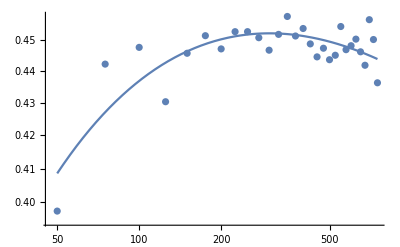

```mathematica
form=p1*(size^(-p2)/Log[size]^(1*p3));vars={p1,p2,p3};
fit=FindFit[fractionOfMissclassificationsResultsMean,form,vars,size]
form/.fit
Show[
ListLogLogPlot[fractionOfMissclassificationsResultsMean]
,
LogLogPlot[form/.fit,{size,nMin,nMax}]
]
```

```mathematica
Clear[str];
scale=0.6;

str="\\begin{tikzpicture}[scale="<>ToString[N[scale]]<>"]\n";

str=str<>"\\begin{axis}[\n";
str=str<>"%\txmode = log, xmin = "<>ToString[N[fractionOfMissclassificationsResultsMean[[1,1]]]]<>", xmax = "<>ToString[N[fractionOfMissclassificationsResultsMean[[-1,1]]]]<>",\n";
str=str<>"%\tymode = log, ymin = 0, ymax = 1,\n";
str=str<>"\txlabel=$n$, ylabel={Fraction of misclassified vertices}\n";
str=str<>"]\n";

str=str<>"\addplot[mark=x,only marks,error bars/.cd, y dir=both, y explicit] plot coordinates {\n";
For[i=1,i≤Length[fractionOfMissclassificationsResultsMean],i++,

x=fractionOfMissclassificationsResultsMean[[i,1]];
y=fractionOfMissclassificationsResultsMean[[i,2]];
confHi=-y+fractionOfMissclassificationsResultsMeanPlusStd[[i,2]];
confLo=confHi;

str=str<>"\t("<>ToString[N[x]]<>","<>ToString[N[y]]<>")";
str=str<>" += ("<>ToString[N[x]]<>","<>ToString[N[confHi]]<>")";
str=str<>" -= ("<>ToString[N[x]]<>","<>ToString[N[confLo]]<>")\n";
];
str=str<>"};\n";
str=str<>"\end{axis}\n";
str=str<>"\end{tikzpicture}\n";

str
```

\begin{tikzpicture}[scale=0.6]
\begin{axis}[
%	xmode = log, xmin = 50., xmax = 750.,
%	ymode = log, ymin = 0, ymax = 1,
	xlabel=$n$, ylabel={Fraction of misclassified vertices}
]
\addplot[mark=x,only marks,error bars/.cd, y dir=both, y explicit] plot coordinates {
	(50.,0.3975) += (50.,0.0267251) -= (50.,0.0267251)
	(75.,0.442333) += (75.,0.0200714) -= (75.,0.0200714)
	(100.,0.44775) += (100.,0.0252016) -= (100.,0.0252016)
	(125.,0.4304) += (125.,0.0210899) -= (125.,0.0210899)
	(150.,0.445833) += (150.,0.0188935) -= (150.,0.0188935)
	(175.,0.451571) += (175.,0.0190072) -= (175.,0.0190072)
	(200.,0.44725) += (200.,0.01283) -= (200.,0.01283)
	(225.,0.452889) += (225.,0.012231) -= (225.,0.012231)
	(250.,0.4529) += (250.,0.012029) -= (250.,0.012029)
	(275.,0.450909) += (275.,0.0122723) -= (275.,0.0122723)
	(300.,0.446833) += (300.,0.0114004) -= (300.,0.0114004)
	(325.,0.452) += (325.,0.0136182) -= (325.,0.0136182)
	(350.,0.457929) += (350.,0.00991431) -= (350.,0.00991431)
	(375.,0.451467) += (375.,0.011987) -= (375.,0.011987)
	(400.,0.453938) += (400.,0.0108425) -= (400.,0.0108425)
	(425.,0.448882) += (425.,0.0100245) -= (425.,0.0100245)
	(450.,0.444667) += (450.,0.00997344) -= (450.,0.00997344)
	(475.,0.447474) += (475.,0.00822297) -= (475.,0.00822297)
	(500.,0.44375) += (500.,0.00879182) -= (500.,0.00879182)
	(525.,0.44519) += (525.,0.00788072) -= (525.,0.00788072)
	(550.,0.454591) += (550.,0.00887242) -= (550.,0.00887242)
	(575.,0.447) += (575.,0.00895271) -= (575.,0.00895271)
	(600.,0.448292) += (600.,0.00817759) -= (600.,0.00817759)
	(625.,0.45044) += (625.,0.00926881) -= (625.,0.00926881)
	(650.,0.446308) += (650.,0.00995441) -= (650.,0.00995441)
	(675.,0.441963) += (675.,0.00804083) -= (675.,0.00804083)
	(700.,0.456857) += (700.,0.00940801) -= (700.,0.00940801)
	(725.,0.45031) += (725.,0.00713299) -= (725.,0.00713299)
	(750.,0.436367) += (750.,0.00710811) -= (750.,0.00710811)
};
\end{axis}
\end{tikzpicture}

```mathematica
(* Loop over T. *)
Remove["Global`*"];
OUTPUT=True;

α={0.15,0.35,0.5};α/=Total[α];
p12=0.2;p13=0.3;
p21=0.1;p23=0.2;
p31=0.35;p32=0.05;
p={
{1-p12-p13,p12,p13},
{p21,1-p21-p23,p23},
{p31,p32,1-p31-p32}
};

α={0.15,0.35,0.5};α/=Total[α];
p12=0.045;p13=0.035;
p21=0.0125;p23=0.09;
p31=0.0175;p32=0.020;
p={
{1-p12-p13,p12,p13},
{p21,1-p21-p23,p23},
{p31,p32,1-p31-p32}
};

α={1/3,1/3,1/3}//N;α/=Total[α];
p12=0.4;p13=0.5;
p21=0.7;p23=0.2;
p31=0.6;p32=0.3;
p={
{1-p12-p13,p12,p13},
{p21,1-p21-p23,p23},
{p31,p32,1-p31-p32}
};

α
p//MatrixForm


(* Check clusterability. *)
K=Length[α];
If[K==2,β=First[{β1,β2}/.Solve[{β1,β2}.p=={β1,β2}&&β1+β2==1,{β1,β2}]]];
If[K==3,β=First[{β1,β2,β3}/.Solve[{β1,β2,β3}.p=={β1,β2,β3}&&β1+β2+β3==1,{β1,β2,β3}]]];

Iab=Function[{a,b},
(1/α[[a]])^1*Sum[β[[a]]*p[[a,k]]*Log[p[[a,k]]/p[[b,k]]]+β[[k]]*p[[k,a]]*Log[(p[[k,a]]/p[[k,b]])*(α[[b]]/α[[a]])^1],{k,1,K}]
+(β[[b]]/α[[b]]-β[[a]]/α[[a]])
];

If[K==2,Iαβp=Min[Iab[1,2],Iab[2,1]];];
If[K==3,Iαβp=Min[Iab[1,2],Iab[1,3],Iab[2,1],Iab[2,3],Iab[3,1],Iab[3,2]];];

Print["I(α,β,p) = ",Iαβp];
If[Iαβp>0,
Print["Positive, so these parameters are clusterable."];
,
Print["NOT positive, so these parameters are NOT clusterable."];
];


fractionOfMissclassificationsResults={};
fractionOfMissclassificationsResultsMean={};
fractionOfMissclassificationsResultsStd={};
fractionOfMissclassificationsResultsMeanPlusStd={};
fractionOfMissclassificationsResultsMeanMinusStd={};

fractionOfMissclassificationsResultsImproved={};
fractionOfMissclassificationsResultsImprovedMean={};
fractionOfMissclassificationsResultsImprovedStd={};
fractionOfMissclassificationsResultsImprovedMeanPlusStd={};
fractionOfMissclassificationsResultsImprovedMeanMinusStd={};

fractionOfMissclassificationsResultsImproved2={};
fractionOfMissclassificationsResultsImproved2Mean={};
fractionOfMissclassificationsResultsImproved2Std={};
fractionOfMissclassificationsResultsImproved2MeanPlusStd={};
fractionOfMissclassificationsResultsImproved2MeanMinusStd={};

Print[ProgressIndicator[Dynamic[(T-TMin)/(TMax-TMin)]]];
Print[ProgressIndicator[Dynamic[sample/numberOfSamples]]];

OUTPUT=False;

If[OUTPUT==True,

Print[
Dynamic[
Show[
ListLogLogPlot[fractionOfMissclassificationsResultsMean,Joined->True,Mesh->Full,
PlotRange->{0.9*Transpose[fractionOfMissclassificationsResultsMean][[2]]//Min,1.1*Transpose[fractionOfMissclassificationsResultsMeanPlusStd][[2]]//Max}]
,
ListLogLogPlot[fractionOfMissclassificationsResultsMeanPlusStd,Joined->True,PlotStyle->Dashed,
PlotRange->{0.9*Transpose[fractionOfMissclassificationsResultsMean][[2]]//Min,1.1*Transpose[fractionOfMissclassificationsResultsMeanPlusStd][[2]]//Max}]
,
ListLogLogPlot[fractionOfMissclassificationsResultsMeanMinusStd,Joined->True,PlotStyle->Dashed,
PlotRange->{0.9*Transpose[fractionOfMissclassificationsResultsMean][[2]]//Max,1.1*Transpose[fractionOfMissclassificationsResultsMeanPlusStd][[2]]//Max}]
]
]
];

Print[
Dynamic[
Show[
ListLogLogPlot[fractionOfMissclassificationsResultsImprovedMean,Joined->True,Mesh->Full,
PlotRange->{0.9*Transpose[fractionOfMissclassificationsResultsImprovedMean][[2]]//Min,1.1*Transpose[fractionOfMissclassificationsResultsImprovedMeanPlusStd][[2]]//Max}]
,
ListLogLogPlot[fractionOfMissclassificationsResultsImprovedMeanPlusStd,Joined->True,PlotStyle->Dashed,
PlotRange->{0.9*Transpose[fractionOfMissclassificationsResultsImprovedMean][[2]]//Min,1.1*Transpose[fractionOfMissclassificationsResultsImprovedMeanPlusStd][[2]]//Max}]
,
ListLogLogPlot[fractionOfMissclassificationsResultsImprovedMeanMinusStd,Joined->True,PlotStyle->Dashed,
PlotRange->{0.9*Transpose[fractionOfMissclassificationsResultsImprovedMean][[2]]//Max,1.1*Transpose[fractionOfMissclassificationsResultsImprovedMeanPlusStd][[2]]//Max}]
]
]
];

Print[
Dynamic[
Show[
ListLogLogPlot[fractionOfMissclassificationsResultsImproved2Mean,Joined->True,Mesh->Full,
PlotRange->{0.9*Transpose[fractionOfMissclassificationsResultsImproved2Mean][[2]]//Min,1.1*Transpose[fractionOfMissclassificationsResultsImproved2MeanPlusStd][[2]]//Max}]
,
ListLogLogPlot[fractionOfMissclassificationsResultsImproved2MeanPlusStd,Joined->True,PlotStyle->Dashed,
PlotRange->{0.9*Transpose[fractionOfMissclassificationsResultsImproved2Mean][[2]]//Min,1.1*Transpose[fractionOfMissclassificationsResultsImproved2MeanPlusStd][[2]]//Max}]
,
ListLogLogPlot[fractionOfMissclassificationsResultsImproved2MeanMinusStd,Joined->True,PlotStyle->Dashed,
PlotRange->{0.9*Transpose[fractionOfMissclassificationsResultsImproved2Mean][[2]]//Max,1.1*Transpose[fractionOfMissclassificationsResultsImproved2MeanPlusStd][[2]]//Max}]
]
]
];

];

Print["Initial samples: ",Dynamic[misclassificationSamples//Mean//N]];
Print["Improved 1 samples: ",Dynamic[misclassificationSamplesImproved//Mean//N]];
Print["Improved 2 samples: ",Dynamic[misclassificationSamplesImproved2//Mean//N]];

Print["Initial samples: ",Dynamic[misclassificationSamples//N]];
Print["Improved 1 samples: ",Dynamic[misclassificationSamplesImproved//N]];
Print["Improved 2 samples: ",Dynamic[misclassificationSamplesImproved2//N]];

Print["Improving cluster allocation: ",ProgressIndicator[Dynamic[(improvement-1)/(maxImprovements-1)]]];
Print["Executing improvement ",Dynamic[improvement],"... At ",Dynamic[N[100*(x-1)/(n-1),3]],"%."];

Print["Starting simulations..."];
tic=AbsoluteTime[];

(*
n=225;
TMin=Ceiling[n^1.1*Log[n]]//N;
TMax=Ceiling[n^1.6*Log[n]]//N;
TDelta=Ceiling[(TMax-TMin)/10]//N;
numberOfSamples=10;
*)
n=240;
TMin=2500;
TMax=30000;
TDelta=2500;
numberOfSamples=100;
For[T=TMin,T≤TMax,T+=TDelta,

Pause[0.5];

misclassificationSamples={};
misclassificationSamplesImproved={};
misclassificationSamplesImproved2={};
For[sample=1,sample≤numberOfSamples,sample++,

(* Generate clusters randomly. *)
Clear[numberOfClusters,clusterAssignment,clusterSizes,σ];
numberOfClusters=Length[α];
clusterAssignment=RandomChoice[α->Table[k,{k,1,numberOfClusters}],n]//Sort;
clusterSizes=Table[Count[clusterAssignment,k],{k,1,numberOfClusters}];
σ=Function[v,clusterAssignment[[v]]];

(* Construct the P-matrix. *)
Clear[P,r,c];
P=Table[0,{v,1,n},{w,1,n}];
For[r=1,r≤n,r++,
For[c=1,c≤n,c++,
P[[r,c]]=If[r≠c,1,0]*p[[σ[r],σ[c]]]/(clusterSizes[[σ[c]]]-If[σ[r]==σ[c],1,0]);
];
];

(* Markov chain. *)
x0=RandomInteger[{1,n}];
tMin=0;tMax=Ceiling[T];
OUTPUT=False;

Nhat=0*P;
currentState=x0;

(* Warmup. *)
For[t=tMin,t≤Ceiling[n*Log[n]],t++,
nextState=RandomChoice[P[[currentState,;;]]->Table[y,{y,1,n}]];
currentState=nextState;
];
For[t=tMin,t≤tMax,t++,

(* Generate the next state randomly. *)
nextState=RandomChoice[P[[currentState,;;]]->Table[y,{y,1,n}]];

If[OUTPUT,
Print["At t = ",t,", the process jumps from ",currentState," to ",nextState,"."];
];

(* Record the transition. *)
Nhat[[currentState,nextState]]+=1;

(* Update the current state. *)
currentState=nextState;
];


(* Normalize observation vectors. *)
Phat=Table[If[Total[Nhat[[r,;;]]]≠0,Nhat[[r,;;]]/Total[Nhat[[r,;;]]],0*Nhat[[r,;;]]],{r,1,n}];


SpectralClusteringSVD=Function[{Phat,kSC},
{Uhat,Σhat,Vhat}=SingularValueDecomposition[Phat];
Rhat=Uhat[[;;,1;;numberOfClusters]].Σhat[[1;;numberOfClusters,1;;numberOfClusters]].Transpose[Vhat[[;;,1;;numberOfClusters]]];

(*
ClusteringComponents[Rhat,kSC,1,Method->"KMeans"]
*)

numberOfSeeds=5;
bestObjective=Infinity;
For[seed=1,seed≤numberOfSeeds,seed++,

(* Generate cluster structure with KMeans and the seed. *)
currentTuple=ClusteringComponents[Rhat,kSC,1,Method->"KMeans","RandomSeed"->seed];

centroids={};
For[cluster=1,cluster≤K,cluster++,
positions=Position[currentTuple,cluster]//Flatten;
AppendTo[centroids,Mean[Rhat[[positions,;;]]]];
];

objectiveValue=Sum[Norm[Rhat[[x]]-centroids[[currentTuple[[x]]]],2]^2,{x,1,n}];

If[objectiveValue<bestObjective,
bestObjective=objectiveValue;
bestAssignment=currentTuple;
];
];

bestAssignment
];


inputMatrix=Nhat;
recoveredClusterAssignment=SpectralClusteringSVD[inputMatrix,numberOfClusters];

Pause[1];


MissclassificationsStatistics=Function[recoveredClusterAssignment,

(* Find the best permutation of recovered clusters. *)
numberOfMissclassifiedVertices=Sum[If[recoveredClusterAssignment[[r]]≠clusterAssignment[[r]],1,0],{r,1,n}];

minNumberOfMissclassifiedVertices=n;
permutations=Permutations[Table[cluster,{cluster,1,numberOfClusters}]];
For[index=1,index≤Length[permutations],index++,
reordering=Table[
permutations[[index,recoveredClusterAssignment[[r]]]]
,
{r,1,n}];

numberOfMissclassifiedVertices=Sum[If[reordering[[r]]≠clusterAssignment[[r]],1,0],{r,1,n}];

If[numberOfMissclassifiedVertices≤minNumberOfMissclassifiedVertices,
minRecoveredClusterAssignment=reordering;
minNumberOfMissclassifiedVertices=numberOfMissclassifiedVertices;
];
];

{minNumberOfMissclassifiedVertices,minRecoveredClusterAssignment}
];


SuccessiveImprovements=Function[{Phat,Nhat,T,recoveredClusterAssignment,maxImprovements},

recoveredClusterSizes=Table[Sum[If[recoveredClusterAssignment[[r]]==cluster,1,0],{r,1,n}],{cluster,1,numberOfClusters}];

(* Estimate pHat: the cluster parameters. *)
S0=Table[Position[recoveredClusterAssignment,cluster]//Flatten,{cluster,1,numberOfClusters}];

(* Version 2. *)
S0sizes=Table[Length[S0[[i]]],{i,1,Length[S0]}];
pHat=Table[
((S0sizes[[cc]]-If[cr==cc,1,0])/(S0sizes[[cr]]*S0sizes[[cc]]))
*Sum[
x=S0[[cr,xIndex]];y=S0[[cc,yIndex]];
Phat[[x,y]]
,{xIndex,1,Length[S0[[cr]]]}
,{yIndex,1,Length[S0[[cc]]]}
]
,{cr,1,numberOfClusters},{cc,1,numberOfClusters}];
αHat=clusterSizes/n//N;
βHat=(1/T)*Table[
Sum[
x=S0[[cr,xIndex]];
(*Total[Nhat[[;;,x]]]*) (* OK due to global balance! See remark on p. 83 notebook. *)
Total[Nhat[[x,;;]]]
,
{xIndex,1,Length[S0[[cr]]]}]
,{cr,1,numberOfClusters}
];

(* Improvement loop. *)
St=S0;
latestClusterAssignment=recoveredClusterAssignment;
latestClusterSizes=recoveredClusterSizes;
For[improvement=1,improvement≤maxImprovements,improvement++,

nextClusterAssignment={};
Stp1=Table[{},{c,1,numberOfClusters}];

For[x=1,x≤n,x++,

(* Version 6. *)
clusterShifts=
Table[
Sum[
clusterOfx=latestClusterAssignment[[x]];
clusterOfy=latestClusterAssignment[[y]];
If[y≠x,
1*Nhat[[x,y]]*Log[pHat[[cluster,clusterOfy]]]
+
1*Nhat[[y,x]]*Log[pHat[[clusterOfy,cluster]]/αHat[[cluster]]^1]
,0
]
,{y,1,n}]
+1*(T/n)*(-βHat[[cluster]]/αHat[[cluster]])
,{cluster,1,numberOfClusters}
];
(*Print["Cluster shift table: ",clusterShifts];*)


maximizingCluster=Flatten[Position[clusterShifts,Max[clusterShifts]]]//First;

AppendTo[nextClusterAssignment,maximizingCluster];
AppendTo[Stp1[[maximizingCluster]],x];

];

latestClusterAssignment=nextClusterAssignment;
latestClusterSizes=Table[Sum[If[latestClusterAssignment[[r]]==cluster,1,0],{r,1,n}],{cluster,1,numberOfClusters}];
St=Stp1;

(* Update pHat, αHat, βHat. *)
pHat=Table[
Sum[
x=St[[cr,xIndex]];y=St[[cc,yIndex]];
Nhat[[x,y]]
,{xIndex,1,Length[St[[cr]]]}
,{yIndex,1,Length[St[[cc]]]}
]
/
Sum[
x=St[[cr,xIndex]];
Nhat[[x,y]]
,{xIndex,1,Length[St[[cr]]]}
,{y,1,n}
]
,{cr,1,numberOfClusters},{cc,1,numberOfClusters}];
αHat=latestClusterSizes/n//N;
βHat=(1/T)*Table[
Sum[
x=St[[cr,xIndex]];
(*Total[Nhat[[;;,x]]]*) (* OK due to global balance! See remark on p. 83 notebook. *)
Total[Nhat[[x,;;]]]
,
{xIndex,1,Length[St[[cr]]]}]
,{cr,1,numberOfClusters}
];

];

{latestClusterAssignment,St}
];

improvedClusterAssignment=SuccessiveImprovements[Phat,Nhat,tMax,recoveredClusterAssignment,1]//First;
orderedImprovedClusterAssignment=MissclassificationsStatistics[improvedClusterAssignment]//Last;
improvedClusterAssignment=orderedImprovedClusterAssignment;

improvedClusterAssignment2=SuccessiveImprovements[Phat,Nhat,tMax,improvedClusterAssignment,1]//First;
orderedImprovedClusterAssignment2=MissclassificationsStatistics[improvedClusterAssignment2]//Last;
improvedClusterAssignment2=orderedImprovedClusterAssignment2;

nrOfMissclassifications=First[MissclassificationsStatistics[recoveredClusterAssignment]];
nrOfMissclassificationsImproved=First[MissclassificationsStatistics[improvedClusterAssignment]];
nrOfMissclassificationsImproved2=First[MissclassificationsStatistics[improvedClusterAssignment2]];

AppendTo[misclassificationSamples,nrOfMissclassifications/n];
AppendTo[misclassificationSamplesImproved,nrOfMissclassificationsImproved/n];
AppendTo[misclassificationSamplesImproved2,nrOfMissclassificationsImproved2/n];

(*If[nrOfMissclassifications==0,Break[]];*)
];

Pause[0.5];

(*If[nrOfMissclassifications==0,Break[]];*)

AppendTo[fractionOfMissclassificationsResults,{T,misclassificationSamples}];
AppendTo[fractionOfMissclassificationsResultsMean,{T,Mean[misclassificationSamples]}];
AppendTo[fractionOfMissclassificationsResultsStd,{T,StandardDeviation[misclassificationSamples]}];
AppendTo[fractionOfMissclassificationsResultsMeanPlusStd,{T,Mean[misclassificationSamples]+2StandardDeviation[misclassificationSamples]/Sqrt[Length[misclassificationSamples]]}];
AppendTo[fractionOfMissclassificationsResultsMeanMinusStd,{T,Mean[misclassificationSamples]-2StandardDeviation[misclassificationSamples]/Sqrt[Length[misclassificationSamples]]}];

Pause[0.5];

AppendTo[fractionOfMissclassificationsResultsImproved,{T,misclassificationSamplesImproved}];
AppendTo[fractionOfMissclassificationsResultsImprovedMean,{T,Mean[misclassificationSamplesImproved]}];
AppendTo[fractionOfMissclassificationsResultsImprovedStd,{T,StandardDeviation[misclassificationSamplesImproved]}];
AppendTo[fractionOfMissclassificationsResultsImprovedMeanPlusStd,{T,Mean[misclassificationSamplesImproved]+2StandardDeviation[misclassificationSamplesImproved]/Sqrt[Length[misclassificationSamplesImproved]]}];
AppendTo[fractionOfMissclassificationsResultsImprovedMeanMinusStd,{T,Mean[misclassificationSamplesImproved]-2StandardDeviation[misclassificationSamplesImproved]/Sqrt[Length[misclassificationSamplesImproved]]}];

Pause[0.5];

AppendTo[fractionOfMissclassificationsResultsImproved2,{T,misclassificationSamplesImproved2}];
AppendTo[fractionOfMissclassificationsResultsImproved2Mean,{T,Mean[misclassificationSamplesImproved2]}];
AppendTo[fractionOfMissclassificationsResultsImproved2Std,{T,StandardDeviation[misclassificationSamplesImproved2]}];
AppendTo[fractionOfMissclassificationsResultsImproved2MeanPlusStd,{T,Mean[misclassificationSamplesImproved2]+2StandardDeviation[misclassificationSamplesImproved2]/Sqrt[Length[misclassificationSamplesImproved2]]}];
AppendTo[fractionOfMissclassificationsResultsImproved2MeanMinusStd,{T,Mean[misclassificationSamplesImproved2]-2StandardDeviation[misclassificationSamplesImproved2]/Sqrt[Length[misclassificationSamplesImproved2]]}];

Pause[0.5];

];
toc=AbsoluteTime[];

Print["Simulation duration was ",toc-tic,"s."];
```

{0.333333,0.333333,0.333333}

(0.1 | 0.4 | 0.5
0.7 | 0.1 | 0.2
0.6 | 0.3 | 0.1)

I(α,β,p) = 0.271658

Positive, so these parameters are clusterable.

Initial samples:

Improved 1 samples:

Improved 2 samples:

Initial samples:

Improved 1 samples:

Improved 2 samples:

Improving cluster allocation:

Executing improvement ... At %.

Starting simulations...

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Simulation duration was 6501.5736611s.

```mathematica
fractionOfMissclassificationsResults//N
fractionOfMissclassificationsResultsImproved//N
fractionOfMissclassificationsResultsImproved2//N
```

{{2500.,{0.370833,0.470833,0.4,0.504167,0.366667,0.316667,0.445833,0.454167,0.333333,0.4625,0.354167,0.454167,0.325,0.4125,0.429167,0.3125,0.466667,0.395833,0.266667,0.358333,0.479167,0.375,0.416667,0.3875,0.3125,0.379167,0.3375,0.3625,0.475,0.4875,0.370833,0.358333,0.383333,0.4375,0.383333,0.329167,0.495833,0.370833,0.3375,0.425,0.433333,0.3375,0.3625,0.345833,0.333333,0.483333,0.404167,0.3125,0.379167,0.395833,0.445833,0.429167,0.341667,0.395833,0.4125,0.445833,0.2875,0.375,0.391667,0.3625,0.345833,0.358333,0.354167,0.35,0.333333,0.3,0.504167,0.329167,0.495833,0.4375,0.391667,0.420833,0.333333,0.4375,0.4625,0.283333,0.441667,0.445833,0.358333,0.466667,0.433333,0.358333,0.491667,0.358333,0.366667,0.375,0.341667,0.325,0.295833,0.366667,0.458333,0.4125,0.354167,0.391667,0.320833,0.3625,0.3625,0.483333,0.479167,0.433333}},{5000.,{0.425,0.245833,0.308333,0.408333,0.316667,0.416667,0.120833,0.3125,0.395833,0.1625,0.266667,0.275,0.3375,0.3,0.475,0.2875,0.245833,0.3,0.329167,0.4625,0.204167,0.454167,0.383333,0.279167,0.366667,0.329167,0.3,0.3125,0.295833,0.333333,0.2625,0.325,0.454167,0.3875,0.320833,0.458333,0.408333,0.325,0.2625,0.229167,0.325,0.266667,0.329167,0.395833,0.333333,0.333333,0.241667,0.420833,0.3125,0.445833,0.320833,0.4,0.454167,0.4625,0.429167,0.320833,0.4375,0.291667,0.316667,0.304167,0.333333,0.2625,0.4625,0.495833,0.4125,0.229167,0.320833,0.291667,0.216667,0.466667,0.420833,0.283333,0.345833,0.333333,0.466667,0.225,0.291667,0.441667,0.283333,0.408333,0.445833,0.275,0.3125,0.329167,0.283333,0.245833,0.304167,0.420833,0.229167,0.383333,0.304167,0.275,0.304167,0.2125,0.325,0.475,0.204167,0.233333,0.3125,0.441667}},{7500.,{0.254167,0.270833,0.404167,0.475,0.2625,0.333333,0.491667,0.35,0.2625,0.283333,0.466667,0.245833,0.333333,0.445833,0.354167,0.404167,0.266667,0.241667,0.295833,0.4125,0.325,0.495833,0.433333,0.266667,0.3125,0.325,0.316667,0.3125,0.416667,0.266667,0.416667,0.204167,0.470833,0.270833,0.420833,0.329167,0.441667,0.133333,0.2125,0.220833,0.320833,0.204167,0.316667,0.225,0.275,0.295833,0.2875,0.483333,0.341667,0.283333,0.325,0.445833,0.3,0.291667,0.333333,0.2875,0.279167,0.470833,0.470833,0.233333,0.470833,0.458333,0.266667,0.3875,0.466667,0.4375,0.245833,0.2625,0.466667,0.304167,0.245833,0.479167,0.2,0.220833,0.279167,0.4375,0.25,0.1875,0.0916667,0.425,0.229167,0.345833,0.233333,0.416667,0.275,0.4625,0.441667,0.4875,0.404167,0.395833,0.2625,0.1375,0.458333,0.4125,0.3,0.329167,0.279167,0.4875,0.225,0.270833}},{10000.,{0.179167,0.4625,0.283333,0.245833,0.125,0.225,0.270833,0.2125,0.241667,0.425,0.404167,0.283333,0.470833,0.479167,0.291667,0.416667,0.0791667,0.166667,0.325,0.283333,0.25,0.491667,0.466667,0.45,0.0958333,0.341667,0.470833,0.458333,0.445833,0.2625,0.454167,0.2875,0.291667,0.291667,0.308333,0.491667,0.3,0.258333,0.283333,0.441667,0.195833,0.333333,0.308333,0.254167,0.208333,0.270833,0.4,0.2875,0.220833,0.45,0.266667,0.4375,0.408333,0.479167,0.325,0.15,0.35,0.304167,0.283333,0.45,0.320833,0.445833,0.179167,0.479167,0.479167,0.2125,0.470833,0.4625,0.3875,0.158333,0.195833,0.320833,0.45,0.3125,0.183333,0.2125,0.429167,0.466667,0.4625,0.479167,0.258333,0.470833,0.216667,0.320833,0.366667,0.295833,0.475,0.308333,0.291667,0.183333,0.208333,0.304167,0.320833,0.195833,0.075,0.145833,0.458333,0.216667,0.320833,0.416667}},{12500.,{0.416667,0.408333,0.225,0.2125,0.0875,0.175,0.270833,0.4625,0.204167,0.233333,0.329167,0.0791667,0.475,0.258333,0.2625,0.333333,0.170833,0.254167,0.1875,0.170833,0.3625,0.2375,0.204167,0.120833,0.4125,0.220833,0.233333,0.0625,0.208333,0.479167,0.133333,0.208333,0.325,0.266667,0.470833,0.141667,0.0333333,0.479167,0.229167,0.25,0.4875,0.470833,0.308333,0.475,0.366667,0.154167,0.416667,0.15,0.458333,0.279167,0.466667,0.445833,0.125,0.316667,0.479167,0.45,0.233333,0.395833,0.133333,0.475,0.204167,0.458333,0.204167,0.170833,0.2,0.133333,0.483333,0.208333,0.4,0.470833,0.258333,0.308333,0.441667,0.466667,0.1625,0.404167,0.279167,0.2125,0.270833,0.175,0.45,0.1125,0.4625,0.104167,0.470833,0.154167,0.320833,0.166667,0.258333,0.183333,0.266667,0.266667,0.4625,0.3125,0.295833,0.245833,0.145833,0.345833,0.258333,0.4375}},{15000.,{0.133333,0.208333,0.158333,0.158333,0.166667,0.429167,0.166667,0.333333,0.433333,0.075,0.104167,0.195833,0.195833,0.4625,0.125,0.2375,0.179167,0.2375,0.191667,0.1625,0.429167,0.166667,0.183333,0.4375,0.0291667,0.320833,0.266667,0.291667,0.2125,0.0791667,0.220833,0.204167,0.0708333,0.2375,0.0833333,0.108333,0.2125,0.220833,0.283333,0.108333,0.0583333,0.458333,0.120833,0.145833,0.45,0.275,0.25,0.158333,0.15,0.104167,0.458333,0.141667,0.141667,0.0875,0.170833,0.279167,0.15,0.141667,0.166667,0.466667,0.0708333,0.433333,0.179167,0.179167,0.2125,0.308333,0.208333,0.2375,0.429167,0.491667,0.125,0.245833,0.470833,0.129167,0.429167,0.2625,0.120833,0.466667,0.0916667,0.475,0.479167,0.245833,0.220833,0.1125,0.35,0.175,0.2375,0.445833,0.0708333,0.241667,0.479167,0.154167,0.458333,0.158333,0.15,0.0958333,0.120833,0.220833,0.104167,0.0833333}},{17500.,{0.108333,0.116667,0.0958333,0.133333,0.191667,0.0833333,0.4625,0.0916667,0.129167,0.266667,0.15,0.05,0.1375,0.0583333,0.158333,0.166667,0.133333,0.4375,0.0291667,0.229167,0.175,0.129167,0.320833,0.191667,0.141667,0.416667,0.1,0.0583333,0.0583333,0.166667,0.0833333,0.45,0.00833333,0.0833333,0.145833,0.104167,0.0791667,0.0875,0.195833,0.025,0.308333,0.116667,0.141667,0.1875,0.2,0.120833,0.0375,0.195833,0.1375,0.483333,0.266667,0.204167,0.075,0.15,0.225,0.108333,0.470833,0.0916667,0.4875,0.15,0.154167,0.1875,0.0916667,0.0375,0.158333,0.0875,0.05,0.129167,0.154167,0.0541667,0.133333,0.0875,0.133333,0.1375,0.0583333,0.1125,0.308333,0.0666667,0.170833,0.258333,0.0708333,0.0541667,0.470833,0.0666667,0.258333,0.05,0.0458333,0.0791667,0.295833,0.233333,0.220833,0.116667,0.229167,0.241667,0.320833,0.145833,0.45,0.104167,0.191667,0.175}},{20000.,{0.0583333,0.075,0.0875,0.0375,0.0666667,0.116667,0.104167,0.0791667,0.0625,0.0333333,0.0833333,0.458333,0.204167,0.1,0.108333,0.0666667,0.0916667,0.1875,0.495833,0.0458333,0.133333,0.104167,0.166667,0.4375,0.1,0.295833,0.125,0.179167,0.0916667,0.0708333,0.116667,0.204167,0.1125,0.1375,0.254167,0.0791667,0.0583333,0.133333,0.1375,0.0541667,0.108333,0.0541667,0.204167,0.104167,0.0875,0.0583333,0.183333,0.0583333,0.425,0.0166667,0.141667,0.120833,0.1,0.0458333,0.491667,0.05,0.0333333,0.0583333,0.0708333,0.0541667,0.1875,0.104167,0.1125,0.35,0.179167,0.0583333,0.1,0.1,0.075,0.075,0.479167,0.05,0.0416667,0.0791667,0.0916667,0.0625,0.1625,0.0958333,0.0958333,0.0541667,0.0916667,0.0291667,0.283333,0.104167,0.0416667,0.075,0.0458333,0.0833333,0.0666667,0.133333,0.0333333,0.0166667,0.0291667,0.241667,0.0916667,0.0833333,0.0208333,0.45,0.0708333,0.0958333}},{22500.,{0.025,0.0541667,0.0708333,0.1125,0.0708333,0.025,0.304167,0.0458333,0.454167,0.1125,0.0458333,0.1125,0.0875,0.0625,0.0625,0.075,0.0166667,0.0625,0.204167,0.466667,0.0541667,0.0291667,0.0291667,0.0958333,0.108333,0.0291667,0.0458333,0.0333333,0.0125,0.0458333,0.0416667,0.0791667,0.0125,0.1875,0.00833333,0.075,0.183333,0.0875,0.025,0.025,0.0416667,0.0541667,0.0125,0.283333,0.0458333,0.0916667,0.0666667,0.129167,0.0541667,0.0333333,0.0125,0.0916667,0.0708333,0.0375,0.0333333,0.175,0.108333,0.166667,0.295833,0.0166667,0.0833333,0.1,0.0416667,0.05,0.116667,0.104167,0.0625,0.0541667,0.116667,0.0625,0.0833333,0.0333333,0.0541667,0.0958333,0.116667,0.0208333,0.166667,0.0916667,0.0416667,0.0791667,0.1875,0.241667,0.445833,0.00416667,0.3,0.133333,0.0166667,0.129167,0.4625,0.3375,0.0833333,0.0333333,0.120833,0.00833333,0.075,0.05,0.145833,0.133333,0.133333,0.1125}},{25000.,{0.00833333,0.0416667,0.0833333,0.025,0.05,0.183333,0.0791667,0.05,0.075,0.0208333,0.075,0.0416667,0.00416667,0.0375,0.00416667,0.05,0.0958333,0.133333,0.0625,0.05,0.0333333,0.0541667,0.0875,0.0458333,0.0291667,0.0625,0.05,0.1,0.0125,0.0125,0.0708333,0.025,0.0208333,0.0375,0.1,0.0875,0.0166667,0.0375,0.0458333,0.0333333,0.0625,0.0583333,0.158333,0.0625,0.0166667,0.05,0.15,0.1875,0.15,0.0458333,0.120833,0.0708333,0.0833333,0.0166667,0.1,0.0708333,0.125,0.0583333,0.025,0.0625,0.0333333,0.0625,0.0291667,0.341667,0.0833333,0.025,0.05,0.141667,0.495833,0.0375,0.1125,0.00833333,0.170833,0.0375,0.0625,0.225,0.05,0.0125,0.0333333,0.458333,0.0333333,0.0541667,0.00833333,0.0375,0.0333333,0.1125,0.0208333,0.0625,0.0583333,0.120833,0.2875,0.0583333,0.0416667,0.154167,0.00833333,0.025,0.00416667,0.0458333,0.025,0.0708333}},{27500.,{0.0541667,0.0708333,0.0416667,0.,0.0333333,0.0208333,0.0166667,0.05,0.0125,0.0416667,0.1,0.0166667,0.0583333,0.0166667,0.025,0.141667,0.0125,0.0375,0.0333333,0.0458333,0.075,0.0208333,0.1,0.0291667,0.0458333,0.233333,0.0208333,0.0125,0.05,0.0333333,0.0208333,0.05,0.0666667,0.0291667,0.0625,0.00416667,0.0291667,0.104167,0.025,0.0791667,0.0458333,0.0166667,0.145833,0.0125,0.0791667,0.0208333,0.,0.0416667,0.0375,0.05,0.0291667,0.454167,0.0333333,0.05,0.0791667,0.0416667,0.0125,0.0625,0.0125,0.025,0.0166667,0.0166667,0.0208333,0.0666667,0.0208333,0.0416667,0.,0.333333,0.075,0.0166667,0.0166667,0.0375,0.0333333,0.0458333,0.454167,0.00833333,0.025,0.0583333,0.0708333,0.0541667,0.00416667,0.0583333,0.00416667,0.0458333,0.1125,0.0375,0.0291667,0.0458333,0.0166667,0.141667,0.1625,0.0416667,0.0166667,0.0708333,0.3125,0.0125,0.145833,0.025,0.0541667,0.0333333}},{30000.,{0.025,0.0125,0.025,0.025,0.0416667,0.00833333,0.0208333,0.00833333,0.0125,0.0208333,0.0333333,0.0125,0.0375,0.0166667,0.0208333,0.0166667,0.0375,0.0291667,0.0291667,0.0333333,0.0166667,0.00833333,0.0208333,0.0166667,0.0166667,0.0583333,0.025,0.0458333,0.0208333,0.0375,0.0416667,0.00416667,0.025,0.0166667,0.0625,0.0375,0.0458333,0.00833333,0.00416667,0.0375,0.0125,0.0291667,0.0916667,0.0166667,0.0333333,0.0208333,0.0458333,0.0625,0.0166667,0.025,0.,0.0291667,0.0166667,0.,0.0291667,0.0208333,0.0625,0.0416667,0.00833333,0.00416667,0.00833333,0.0208333,0.,0.0333333,0.00833333,0.00833333,0.0166667,0.0208333,0.0375,0.0458333,0.0166667,0.0375,0.0708333,0.0333333,0.00416667,0.05,0.0125,0.00833333,0.0583333,0.0375,0.0291667,0.0416667,0.00416667,0.00833333,0.0375,0.0333333,0.0375,0.0416667,0.0208333,0.025,0.0416667,0.0416667,0.0291667,0.0333333,0.00416667,0.025,0.025,0.0125,0.0291667,0.05}}}

{{2500.,{0.65,0.4,0.333333,0.4125,0.275,0.329167,0.308333,0.425,0.2875,0.3625,0.3125,0.304167,0.229167,0.3375,0.35,0.208333,0.470833,0.3375,0.308333,0.291667,0.3375,0.291667,0.358333,0.320833,0.233333,0.291667,0.270833,0.275,0.458333,0.370833,0.341667,0.241667,0.345833,0.35,0.316667,0.2625,0.366667,0.333333,0.308333,0.3375,0.325,0.275,0.270833,0.2875,0.216667,0.4375,0.266667,0.3375,0.341667,0.270833,0.445833,0.345833,0.266667,0.291667,0.325,0.35,0.325,0.291667,0.316667,0.316667,0.270833,0.245833,0.279167,0.308333,0.308333,0.266667,0.379167,0.233333,0.3375,0.329167,0.358333,0.358333,0.266667,0.358333,0.345833,0.266667,0.345833,0.366667,0.279167,0.366667,0.358333,0.208333,0.479167,0.308333,0.329167,0.3375,0.345833,0.304167,0.229167,0.329167,0.35,0.316667,0.325,0.329167,0.345833,0.308333,0.316667,0.416667,0.341667,0.3875}},{5000.,{0.3375,0.320833,0.270833,0.3375,0.2875,0.325,0.295833,0.304167,0.308333,0.316667,0.25,0.254167,0.295833,0.295833,0.341667,0.266667,0.291667,0.304167,0.258333,0.333333,0.229167,0.433333,0.3125,0.208333,0.3125,0.25,0.166667,0.304167,0.179167,0.304167,0.341667,0.25,0.354167,0.341667,0.279167,0.391667,0.3375,0.158333,0.270833,0.341667,0.283333,0.275,0.3125,0.329167,0.316667,0.275,0.3125,0.3375,0.208333,0.3,0.329167,0.308333,0.316667,0.320833,0.354167,0.279167,0.316667,0.304167,0.266667,0.204167,0.2875,0.254167,0.325,0.325,0.329167,0.275,0.345833,0.216667,0.283333,0.366667,0.341667,0.229167,0.316667,0.254167,0.333333,0.216667,0.220833,0.325,0.283333,0.295833,0.3125,0.304167,0.2375,0.3375,0.320833,0.2875,0.3,0.325,0.1625,0.291667,0.216667,0.233333,0.291667,0.15,0.233333,0.470833,0.2375,0.2625,0.245833,0.308333}},{7500.,{0.154167,0.3,0.325,0.3375,0.266667,0.308333,0.4625,0.308333,0.2875,0.2375,0.3,0.233333,0.308333,0.35,0.2875,0.333333,0.320833,0.2875,0.279167,0.291667,0.320833,0.35,0.345833,0.258333,0.258333,0.220833,0.2375,0.266667,0.2875,0.175,0.316667,0.304167,0.325,0.283333,0.345833,0.245833,0.3375,0.0416667,0.175,0.141667,0.245833,0.0625,0.195833,0.2875,0.2625,0.275,0.1875,0.333333,0.341667,0.2,0.216667,0.3125,0.175,0.145833,0.275,0.179167,0.129167,0.375,0.325,0.3125,0.479167,0.325,0.2,0.291667,0.291667,0.3375,0.15,0.1625,0.316667,0.2,0.3125,0.333333,0.316667,0.15,0.3125,0.3125,0.275,0.304167,0.0291667,0.325,0.266667,0.35,0.295833,0.3125,0.225,0.329167,0.304167,0.329167,0.329167,0.308333,0.229167,0.0625,0.316667,0.3125,0.2375,0.3,0.0625,0.320833,0.116667,0.245833}},{10000.,{0.0333333,0.325,0.145833,0.1875,0.0541667,0.15,0.195833,0.075,0.1375,0.320833,0.3,0.166667,0.345833,0.329167,0.245833,0.320833,0.0125,0.0583333,0.316667,0.3125,0.166667,0.329167,0.354167,0.291667,0.00833333,0.2,0.325,0.320833,0.3125,0.175,0.3375,0.204167,0.270833,0.270833,0.345833,0.3375,0.279167,0.3,0.1875,0.291667,0.0916667,0.304167,0.358333,0.15,0.0541667,0.245833,0.320833,0.133333,0.175,0.3125,0.275,0.304167,0.341667,0.329167,0.3125,0.0791667,0.341667,0.279167,0.3125,0.316667,0.216667,0.308333,0.116667,0.3625,0.3375,0.170833,0.341667,0.3125,0.2875,0.0958333,0.104167,0.241667,0.325,0.316667,0.270833,0.295833,0.329167,0.45,0.3375,0.395833,0.216667,0.3125,0.108333,0.3375,0.295833,0.291667,0.325,0.320833,0.3,0.0875,0.254167,0.329167,0.2375,0.0625,0.00833333,0.179167,0.291667,0.320833,0.3,0.275}},{12500.,{0.304167,0.308333,0.108333,0.304167,0.0125,0.05,0.229167,0.333333,0.266667,0.0583333,0.245833,0.116667,0.320833,0.254167,0.225,0.295833,0.0375,0.2125,0.0666667,0.075,0.291667,0.0791667,0.275,0.0208333,0.3375,0.0875,0.0666667,0.191667,0.129167,0.316667,0.00833333,0.175,0.183333,0.3,0.333333,0.0375,0.,0.325,0.308333,0.320833,0.320833,0.316667,0.0541667,0.329167,0.3375,0.025,0.329167,0.0833333,0.35,0.225,0.3,0.304167,0.125,0.291667,0.333333,0.3375,0.208333,0.308333,0.05,0.291667,0.0625,0.325,0.0583333,0.1125,0.225,0.0166667,0.354167,0.0625,0.345833,0.320833,0.108333,0.133333,0.316667,0.304167,0.129167,0.295833,0.145833,0.104167,0.241667,0.2,0.354167,0.0166667,0.316667,0.0166667,0.341667,0.208333,0.125,0.220833,0.125,0.191667,0.208333,0.225,0.270833,0.2,0.245833,0.1,0.0583333,0.179167,0.158333,0.304167}},{15000.,{0.0125,0.0375,0.191667,0.0458333,0.0208333,0.320833,0.0125,0.133333,0.3,0.00833333,0.,0.0458333,0.075,0.458333,0.0125,0.133333,0.133333,0.304167,0.0958333,0.0958333,0.308333,0.120833,0.15,0.3375,0.,0.270833,0.2,0.295833,0.1875,0.00416667,0.141667,0.166667,0.0833333,0.1125,0.,0.00833333,0.1875,0.0625,0.125,0.00416667,0.00416667,0.325,0.0541667,0.0166667,0.329167,0.195833,0.120833,0.0208333,0.2125,0.0166667,0.316667,0.0208333,0.00416667,0.00416667,0.05,0.0708333,0.0166667,0.0333333,0.0375,0.45,0.,0.304167,0.125,0.170833,0.220833,0.35,0.145833,0.241667,0.308333,0.3125,0.0125,0.075,0.3125,0.125,0.325,0.1375,0.0291667,0.329167,0.025,0.320833,0.4,0.3,0.295833,0.0166667,0.0791667,0.1125,0.25,0.3375,0.00416667,0.133333,0.329167,0.0291667,0.3375,0.025,0.158333,0.0125,0.00833333,0.183333,0.0291667,0.00416667}},{17500.,{0.025,0.00833333,0.00833333,0.0291667,0.0916667,0.00416667,0.320833,0.00833333,0.00416667,0.2,0.0125,0.,0.0208333,0.,0.0791667,0.05,0.0916667,0.3125,0.,0.104167,0.0958333,0.0125,0.120833,0.0208333,0.0166667,0.279167,0.00833333,0.00833333,0.00416667,0.0375,0.,0.291667,0.,0.00416667,0.025,0.00416667,0.00416667,0.,0.0625,0.,0.179167,0.0375,0.025,0.3125,0.0333333,0.00833333,0.0625,0.025,0.183333,0.341667,0.0583333,0.0458333,0.00416667,0.05,0.05,0.025,0.329167,0.00833333,0.341667,0.0875,0.0375,0.179167,0.,0.,0.025,0.0125,0.,0.05,0.0916667,0.00416667,0.0291667,0.0125,0.0333333,0.025,0.,0.0166667,0.0791667,0.,0.1125,0.233333,0.00833333,0.,0.333333,0.00416667,0.0791667,0.00416667,0.00416667,0.0125,0.1375,0.0416667,0.0791667,0.0166667,0.0708333,0.229167,0.233333,0.0875,0.333333,0.00416667,0.158333,0.0291667}},{20000.,{0.,0.,0.00416667,0.,0.,0.00833333,0.00416667,0.00416667,0.00416667,0.,0.,0.354167,0.0208333,0.00833333,0.,0.,0.0125,0.0666667,0.35,0.,0.0125,0.00833333,0.05,0.3125,0.0291667,0.0916667,0.0125,0.141667,0.,0.108333,0.00833333,0.141667,0.0125,0.025,0.05,0.00416667,0.,0.0125,0.216667,0.,0.00416667,0.00833333,0.0125,0.0583333,0.0208333,0.,0.0375,0.,0.325,0.,0.00833333,0.0541667,0.00833333,0.00416667,0.3375,0.,0.,0.,0.,0.,0.05,0.00416667,0.00416667,0.1125,0.0708333,0.00416667,0.00416667,0.0125,0.00833333,0.,0.341667,0.,0.00416667,0.,0.0166667,0.00416667,0.0291667,0.00416667,0.00833333,0.,0.00416667,0.,0.2625,0.0333333,0.,0.,0.,0.,0.,0.00833333,0.,0.,0.,0.05,0.00833333,0.00416667,0.,0.3125,0.,0.00833333}},{22500.,{0.,0.,0.,0.00833333,0.,0.,0.183333,0.0625,0.3375,0.0125,0.,0.,0.00416667,0.00416667,0.,0.,0.,0.,0.0166667,0.341667,0.,0.00416667,0.,0.00416667,0.0166667,0.,0.,0.,0.,0.00833333,0.,0.,0.,0.0458333,0.,0.,0.204167,0.,0.,0.,0.,0.,0.,0.0541667,0.,0.00833333,0.,0.00833333,0.,0.,0.,0.00833333,0.,0.,0.,0.170833,0.025,0.125,0.195833,0.,0.,0.00833333,0.,0.0125,0.,0.00416667,0.,0.,0.0125,0.,0.,0.0208333,0.,0.00833333,0.00416667,0.,0.0125,0.00416667,0.00416667,0.,0.316667,0.129167,0.3,0.,0.333333,0.05,0.,0.,0.329167,0.308333,0.00833333,0.,0.,0.,0.00416667,0.,0.104167,0.00833333,0.0958333,0.0583333}},{25000.,{0.,0.,0.00416667,0.,0.,0.0333333,0.,0.00416667,0.,0.,0.00416667,0.,0.,0.,0.,0.00416667,0.00833333,0.,0.,0.,0.,0.,0.00416667,0.,0.,0.,0.00416667,0.00416667,0.,0.,0.,0.,0.,0.,0.00416667,0.,0.,0.,0.,0.,0.,0.,0.00833333,0.00416667,0.,0.,0.0291667,0.0166667,0.00833333,0.00416667,0.,0.00833333,0.0125,0.,0.0125,0.00416667,0.,0.,0.,0.,0.00416667,0.,0.,0.208333,0.00416667,0.,0.00416667,0.00416667,0.345833,0.,0.,0.,0.0583333,0.,0.,0.0458333,0.,0.,0.,0.345833,0.,0.,0.,0.,0.,0.00833333,0.,0.00416667,0.,0.,0.15,0.,0.,0.133333,0.,0.,0.,0.,0.,0.00416667}},{27500.,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00416667,0.,0.,0.,0.,0.,0.,0.00416667,0.,0.,0.108333,0.,0.,0.00416667,0.,0.,0.,0.,0.,0.,0.,0.,0.00416667,0.,0.,0.,0.,0.0166667,0.,0.,0.,0.,0.,0.,0.,0.00416667,0.358333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.15,0.,0.,0.,0.,0.,0.,0.358333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00416667,0.,0.,0.,0.,0.00416667,0.154167,0.,0.,0.,0.108333,0.,0.00416667,0.,0.,0.}},{30000.,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00416667,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00416667,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}}

{{2500.,{0.65,0.620833,0.329167,0.645833,0.3125,0.316667,0.283333,0.333333,0.2625,0.341667,0.3,0.225,0.204167,0.316667,0.354167,0.1875,0.416667,0.291667,0.15,0.275,0.2875,0.233333,0.345833,0.304167,0.2125,0.308333,0.2625,0.270833,0.370833,0.291667,0.258333,0.208333,0.333333,0.329167,0.3125,0.25,0.3625,0.320833,0.308333,0.329167,0.275,0.258333,0.254167,0.304167,0.220833,0.341667,0.229167,0.308333,0.316667,0.279167,0.225,0.316667,0.2,0.270833,0.333333,0.329167,0.320833,0.316667,0.279167,0.295833,0.254167,0.2,0.258333,0.3,0.291667,0.183333,0.345833,0.233333,0.325,0.295833,0.641667,0.291667,0.241667,0.341667,0.65,0.216667,0.341667,0.333333,0.2625,0.341667,0.333333,0.204167,0.495833,0.308333,0.25,0.333333,0.3125,0.266667,0.179167,0.3125,0.3125,0.295833,0.333333,0.333333,0.329167,0.308333,0.241667,0.275,0.304167,0.35}},{5000.,{0.625,0.291667,0.229167,0.65,0.25,0.641667,0.129167,0.2875,0.6375,0.0916667,0.254167,0.270833,0.270833,0.254167,0.345833,0.258333,0.254167,0.279167,0.216667,0.320833,0.191667,0.316667,0.65,0.133333,0.341667,0.241667,0.25,0.2875,0.141667,0.283333,0.275,0.145833,0.629167,0.625,0.291667,0.175,0.641667,0.0708333,0.275,0.158333,0.254167,0.266667,0.266667,0.641667,0.325,0.2375,0.304167,0.325,0.15,0.620833,0.283333,0.633333,0.316667,0.65,0.625,0.245833,0.6375,0.275,0.245833,0.125,0.291667,0.225,0.6625,0.320833,0.645833,0.25,0.308333,0.145833,0.141667,0.3,0.320833,0.166667,0.3375,0.291667,0.658333,0.108333,0.195833,0.645833,0.2875,0.604167,0.658333,0.308333,0.191667,0.258333,0.258333,0.270833,0.245833,0.625,0.0916667,0.6375,0.1875,0.204167,0.279167,0.116667,0.204167,0.358333,0.133333,0.254167,0.191667,0.6375}},{7500.,{0.166667,0.225,0.608333,0.633333,0.216667,0.3,0.345833,0.625,0.279167,0.175,0.641667,0.216667,0.270833,0.641667,0.625,0.658333,0.254167,0.254167,0.283333,0.625,0.320833,0.65,0.629167,0.258333,0.125,0.3125,0.2,0.25,0.616667,0.125,0.654167,0.279167,0.308333,0.2625,0.65,0.141667,0.645833,0.0208333,0.120833,0.05,0.183333,0.025,0.1,0.225,0.175,0.225,0.133333,0.658333,0.35,0.175,0.166667,0.641667,0.0875,0.0833333,0.241667,0.1375,0.0666667,0.358333,0.645833,0.25,0.395833,0.633333,0.191667,0.641667,0.608333,0.654167,0.1,0.0791667,0.641667,0.108333,0.2875,0.325,0.316667,0.0875,0.2875,0.6375,0.233333,0.166667,0.0125,0.641667,0.2375,0.3375,0.2875,0.641667,0.170833,0.6625,0.625,0.654167,0.6,0.645833,0.204167,0.0208333,0.2875,0.65,0.175,0.208333,0.00833333,0.645833,0.0583333,0.241667}},{10000.,{0.,0.645833,0.0791667,0.1,0.0166667,0.0583333,0.0833333,0.0166667,0.0375,0.654167,0.641667,0.075,0.620833,0.654167,0.104167,0.6375,0.,0.00833333,0.241667,0.3,0.0625,0.658333,0.629167,0.629167,0.00416667,0.170833,0.658333,0.620833,0.641667,0.0291667,0.325,0.170833,0.15,0.25,0.304167,0.658333,0.258333,0.304167,0.120833,0.6,0.0125,0.225,0.35,0.0791667,0.00833333,0.1625,0.658333,0.0333333,0.0583333,0.304167,0.245833,0.6375,0.65,0.654167,0.0625,0.0125,0.333333,0.225,0.304167,0.641667,0.154167,0.645833,0.0541667,0.641667,0.645833,0.120833,0.629167,0.641667,0.6375,0.0208333,0.0458333,0.195833,0.633333,0.275,0.191667,0.125,0.304167,0.325,0.654167,0.320833,0.116667,0.645833,0.05,0.35,0.633333,0.154167,0.654167,0.295833,0.2375,0.05,0.183333,0.295833,0.175,0.0166667,0.00416667,0.1375,0.625,0.266667,0.304167,0.620833}},{12500.,{0.620833,0.625,0.0625,0.233333,0.00416667,0.00833333,0.191667,0.625,0.2875,0.00416667,0.166667,0.0208333,0.645833,0.166667,0.1125,0.295833,0.00833333,0.170833,0.00833333,0.00833333,0.145833,0.00833333,0.225,0.00416667,0.633333,0.00833333,0.0166667,0.0166667,0.025,0.641667,0.,0.129167,0.0958333,0.258333,0.666667,0.,0.,0.6625,0.316667,0.129167,0.645833,0.65,0.00833333,0.654167,0.329167,0.00833333,0.633333,0.00416667,0.620833,0.125,0.641667,0.645833,0.0458333,0.254167,0.645833,0.625,0.2125,0.591667,0.,0.625,0.,0.658333,0.0166667,0.0375,0.1,0.,0.6375,0.00833333,0.308333,0.641667,0.0416667,0.0458333,0.65,0.6125,0.05,0.633333,0.0208333,0.0375,0.1,0.291667,0.2875,0.00416667,0.629167,0.,0.6375,0.2625,0.0166667,0.0958333,0.0375,0.0541667,0.0833333,0.129167,0.6,0.1125,0.0833333,0.025,0.,0.0583333,0.0583333,0.645833}},{15000.,{0.,0.00416667,0.0541667,0.,0.,0.629167,0.,0.0166667,0.633333,0.00416667,0.,0.00833333,0.00833333,0.3,0.00416667,0.05,0.0208333,0.191667,0.00833333,0.0166667,0.6125,0.0166667,0.0291667,0.608333,0.,0.229167,0.108333,0.225,0.0583333,0.,0.0208333,0.025,0.00833333,0.0208333,0.,0.,0.0875,0.00416667,0.0416667,0.00416667,0.,0.620833,0.00416667,0.,0.629167,0.05,0.0208333,0.00833333,0.0291667,0.,0.625,0.,0.,0.,0.00833333,0.00416667,0.,0.,0.,0.308333,0.,0.6375,0.05,0.0416667,0.2,0.170833,0.025,0.241667,0.65,0.629167,0.,0.0125,0.645833,0.0208333,0.583333,0.0333333,0.,0.654167,0.,0.65,0.3375,0.0958333,0.129167,0.,0.00833333,0.0125,0.125,0.65,0.00416667,0.00833333,0.6375,0.,0.658333,0.0125,0.0291667,0.00416667,0.,0.0541667,0.00416667,0.}},{17500.,{0.00833333,0.,0.,0.,0.,0.,0.658333,0.,0.,0.0708333,0.,0.00416667,0.,0.,0.,0.,0.,0.641667,0.,0.0125,0.00416667,0.,0.0125,0.,0.,0.616667,0.,0.,0.,0.00416667,0.,0.629167,0.,0.,0.0125,0.,0.,0.,0.0125,0.,0.0291667,0.00833333,0.,0.216667,0.,0.,0.,0.00416667,0.0291667,0.65,0.00416667,0.00833333,0.00416667,0.,0.00416667,0.,0.633333,0.,0.654167,0.00416667,0.00416667,0.0458333,0.,0.,0.,0.00416667,0.,0.,0.00416667,0.00416667,0.,0.,0.,0.00416667,0.,0.,0.,0.,0.0333333,0.191667,0.,0.,0.616667,0.,0.00416667,0.,0.00416667,0.,0.0291667,0.,0.,0.,0.,0.0208333,0.0541667,0.00833333,0.658333,0.,0.0125,0.}},{20000.,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.6125,0.,0.,0.,0.,0.,0.00416667,0.65,0.,0.,0.,0.00416667,0.3,0.,0.00416667,0.,0.0416667,0.,0.,0.,0.025,0.,0.,0.,0.,0.,0.,0.275,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.645833,0.,0.,0.,0.,0.,0.654167,0.,0.,0.,0.,0.,0.,0.00416667,0.,0.00416667,0.,0.,0.,0.,0.,0.,0.620833,0.,0.,0.,0.,0.,0.00416667,0.,0.,0.,0.,0.,0.166667,0.00416667,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.654167,0.,0.}},{22500.,{0.,0.,0.,0.,0.,0.,0.025,0.,0.6125,0.,0.,0.,0.,0.00416667,0.,0.,0.,0.,0.,0.633333,0.,0.,0.,0.00416667,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.216667,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0666667,0.,0.00416667,0.0583333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.283333,0.025,0.608333,0.,0.1,0.,0.,0.,0.6375,0.295833,0.,0.,0.,0.,0.,0.,0.00833333,0.,0.00416667,0.}},{25000.,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.05,0.00416667,0.,0.,0.,0.645833,0.,0.,0.,0.,0.,0.,0.00416667,0.,0.,0.,0.645833,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0208333,0.,0.,0.00416667,0.,0.,0.,0.,0.,0.}},{27500.,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0125,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.641667,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.6125,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0583333,0.,0.,0.,0.,0.,0.,0.,0.,0.}},{30000.,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}}

```mathematica
Clear[str];
scale=1;

str="\\begin{tikzpicture}[scale="<>ToString[N[scale]]<>"]\n";
str=str<>"\\footnotesize\n";

str=str<>"\\begin{axis}[\n";
str=str<>"\twidth=0.9*\linewidth, height=0.9*0.618\linewidth,\n";
str=str<>"%\txmode = log, xmin = "<>ToString[N[fractionOfMissclassificationsResultsMean[[1,1]]]]<>", xmax = "<>ToString[N[fractionOfMissclassificationsResultsMean[[-1,1]]]]<>",\n";
str=str<>"%\tymode = log, ymin = 0, ymax = 1,\n";
str=str<>"%\tymin = 0, ymax = 0.5,\n";
str=str<>"\txlabel=$T$, ylabel={Fraction of misclassified vertices},\n";
str=str<>"\txtick={0,10000,20000,30000},\n\tscaled x ticks=false\n";
str=str<>"]\n";

str=str<>"\addplot[mark=square*, mark size=0.5em, mark options={fill=white},\n\tx filter/.code={\pgfmathparse{\pgfmathresult+10}},\n\t\tnodes near coords={0},\n\t\tevery node near coord/.style = {font=\scriptsize\sffamily\\bfseries, text=black, anchor=center},\n\t\terror bars/.cd, y dir=both, y explicit] plot coordinates {\n";
For[i=1,i≤Length[fractionOfMissclassificationsResultsMean],i++,
x=fractionOfMissclassificationsResultsMean[[i,1]];
y=fractionOfMissclassificationsResultsMean[[i,2]];
confHi=-y+fractionOfMissclassificationsResultsMeanPlusStd[[i,2]];
confLo=confHi;

str=str<>"\t("<>ToString[N[x]]<>","<>ToString[N[y]]<>")";
str=str<>" += ("<>ToString[N[x]]<>","<>ToString[N[confHi]]<>")";
str=str<>" -= ("<>ToString[N[x]]<>","<>ToString[N[confLo]]<>")\n";
];
str=str<>"};\n";

str=str<>"\addplot[mark=square*, mark size=0.5em, mark options={fill=white},\n\t\tnodes near coords={1},\n\t\tevery node near coord/.style = {font=\scriptsize\sffamily\\bfseries, text=black, anchor=center},\n\t\terror bars/.cd, y dir=both, y explicit] plot coordinates {\n";
For[i=1,i≤Length[fractionOfMissclassificationsResultsImprovedMean],i++,
x=fractionOfMissclassificationsResultsImprovedMean[[i,1]];
y=fractionOfMissclassificationsResultsImprovedMean[[i,2]];
confHi=-y+fractionOfMissclassificationsResultsImprovedMeanPlusStd[[i,2]];
confLo=confHi;

str=str<>"\t("<>ToString[N[x]]<>","<>ToString[N[y]]<>")";
str=str<>" += ("<>ToString[N[x]]<>","<>ToString[N[confHi]]<>")";
str=str<>" -= ("<>ToString[N[x]]<>","<>ToString[N[confLo]]<>")\n";
];
str=str<>"};\n";

str=str<>"\addplot[mark=square*, mark size=0.5em, mark options={fill=white},\n\tx filter/.code={\pgfmathparse{\pgfmathresult-10}},\n\t\tnodes near coords={2},\n\t\tevery node near coord/.style = {font=\scriptsize\sffamily\\bfseries, text=black, anchor=center},\n\t\terror bars/.cd, y dir=both, y explicit] plot coordinates {\n";
For[i=1,i≤Length[fractionOfMissclassificationsResultsImproved2Mean],i++,
x=fractionOfMissclassificationsResultsImproved2Mean[[i,1]];
y=fractionOfMissclassificationsResultsImproved2Mean[[i,2]];
confHi=-y+fractionOfMissclassificationsResultsImproved2MeanPlusStd[[i,2]];
confLo=confHi;

str=str<>"\t("<>ToString[N[x]]<>","<>ToString[N[y]]<>")";
str=str<>" += ("<>ToString[N[x]]<>","<>ToString[N[confHi]]<>")";
str=str<>" -= ("<>ToString[N[x]]<>","<>ToString[N[confLo]]<>")\n";
];
str=str<>"};\n";

str=str<>"\end{axis}\n";
str=str<>"\end{tikzpicture}\n";

str
```

\begin{tikzpicture}[scale=1.]
\footnotesize
\begin{axis}[
	width=0.9*\linewidth, height=0.9*0.618\linewidth,
%	xmode = log, xmin = 2500., xmax = 30000.,
%	ymode = log, ymin = 0, ymax = 1,
%	ymin = 0, ymax = 0.5,
	xlabel=$T$, ylabel={Fraction of misclassified vertices},
	xtick={0,10000,20000,30000},
	scaled x ticks=false
]
\addplot[mark=square*, mark size=0.5em, mark options={fill=white},
	x filter/.code={\pgfmathparse{\pgfmathresult+10}},
		nodes near coords={0},
		every node near coord/.style = {font=\scriptsize\sffamily\bfseries, text=black, anchor=center},
		error bars/.cd, y dir=both, y explicit] plot coordinates {
	(2500.,0.391) += (2500.,0.0115935) -= (2500.,0.0115935)
	(5000.,0.335333) += (5000.,0.0161917) -= (5000.,0.0161917)
	(7500.,0.333542) += (7500.,0.0193248) -= (7500.,0.0193248)
	(10000.,0.323542) += (10000.,0.0224775) -= (10000.,0.0224775)
	(12500.,0.290167) += (12500.,0.0253637) -= (12500.,0.0253637)
	(15000.,0.230667) += (15000.,0.0258024) -= (15000.,0.0258024)
	(17500.,0.168) += (17500.,0.0231834) -= (17500.,0.0231834)
	(20000.,0.126625) += (20000.,0.0221868) -= (20000.,0.0221868)
	(22500.,0.102292) += (22500.,0.0201549) -= (22500.,0.0201549)
	(25000.,0.0754167) += (25000.,0.0163013) -= (25000.,0.0163013)
	(27500.,0.0595417) += (27500.,0.0157871) -= (27500.,0.0157871)
	(30000.,0.0268333) += (30000.,0.00341713) -= (30000.,0.00341713)
};
\addplot[mark=square*, mark size=0.5em, mark options={fill=white},
		nodes near coords={1},
		every node near coord/.style = {font=\scriptsize\sffamily\bfseries, text=black, anchor=center},
		error bars/.cd, y dir=both, y explicit] plot coordinates {
	(2500.,0.325875) += (2500.,0.0126981) -= (2500.,0.0126981)
	(5000.,0.290667) += (5000.,0.0107922) -= (5000.,0.0107922)
	(7500.,0.267333) += (7500.,0.0164488) -= (7500.,0.0164488)
	(10000.,0.2485) += (10000.,0.0202324) -= (10000.,0.0202324)
	(12500.,0.202625) += (12500.,0.0224916) -= (12500.,0.0224916)
	(15000.,0.144208) += (15000.,0.0257592) -= (15000.,0.0257592)
	(17500.,0.0738333) += (17500.,0.0199284) -= (17500.,0.0199284)
	(20000.,0.04325) += (20000.,0.0181491) -= (20000.,0.0181491)
	(22500.,0.039875) += (22500.,0.0178602) -= (22500.,0.0178602)
	(25000.,0.0150417) += (25000.,0.0111727) -= (25000.,0.0111727)
	(27500.,0.012875) += (27500.,0.0111986) -= (27500.,0.0111986)
	(30000.,0.0000833333) += (30000.,0.000117254) -= (30000.,0.000117254)
};
\addplot[mark=square*, mark size=0.5em, mark options={fill=white},
	x filter/.code={\pgfmathparse{\pgfmathresult-10}},
		nodes near coords={2},
		every node near coord/.style = {font=\scriptsize\sffamily\bfseries, text=black, anchor=center},
		error bars/.cd, y dir=both, y explicit] plot coordinates {
	(2500.,0.308208) += (2500.,0.0186608) -= (2500.,0.0186608)
	(5000.,0.331333) += (5000.,0.0359201) -= (5000.,0.0359201)
	(7500.,0.340083) += (7500.,0.0441793) -= (7500.,0.0441793)
	(10000.,0.309583) += (10000.,0.0494197) -= (10000.,0.0494197)
	(12500.,0.249292) += (12500.,0.0525498) -= (12500.,0.0525498)
	(15000.,0.14375) += (15000.,0.0467067) -= (15000.,0.0467067)
	(17500.,0.066375) += (17500.,0.0367634) -= (17500.,0.0367634)
	(20000.,0.04675) += (20000.,0.0313558) -= (20000.,0.0313558)
	(22500.,0.035875) += (22500.,0.0258825) -= (22500.,0.0258825)
	(25000.,0.01375) += (25000.,0.0181829) -= (25000.,0.0181829)
	(27500.,0.01325) += (27500.,0.0176715) -= (27500.,0.0176715)
	(30000.,0.) += (30000.,0.) -= (30000.,0.)
};
\end{axis}
\end{tikzpicture}